# Numerical Evaluation of Kalnajs Basis Functions

This script is designed to output the Kalnajs basis functions to arbitrary order so that I can use them in linear response calculations.

## General Definitions

```mathematica
Subscript[k, ka] = 4;
Subscript[R, ka]= 20;
```

## Potential Functions

For these functions, we assume that r has already been normalised (i.e. divided by R_ka) so that 0≤r≤1.

```mathematica
𝒫[n_,ℓ_] := 𝒫[n,ℓ] = (((2 Subscript[k, ka] +ℓ +2n +1/2)Gamma[(2 Subscript[k, ka] +ℓ +n +1/2)]Gamma[.0bℓ+n+(1/2)])/(Gamma[2 Subscript[k, ka]+n+1](Gamma[ℓ+1])^2 Gamma[n+1]))^(1/2);
α[i_, j_,n_, ℓ_] :=α[i, j,n, ℓ]=( Pochhammer[-Subscript[k, ka],i]Pochhammer[ℓ+1/2,i]Pochhammer[2 Subscript[k, ka]+ℓ+n+1/2,j]Pochhammer[i+ℓ+1/2,j]Pochhammer[-n,j])/(Pochhammer[ℓ+1,i]Pochhammer[1,i]Pochhammer[ℓ+i+1,j]Pochhammer[ℓ+1/2,j]Pochhammer[1,j]);
𝒰[r_,n_,ℓ_] := If[r==0,0,- (𝒫[n, ℓ] r^ℓ)/Subscript[R, ka]^(1/2)Sum[ α[i,j,n,ℓ] r^(2i+2j), {i, 0, Subscript[k, ka]}, {j, 0, n}]];
```

## Density Functions

```mathematica
𝒮[n_,ℓ_] :=𝒮[n,ℓ] = Gamma[Subscript[k, ka]+1]/(π Gamma[2 Subscript[k, ka]+1]Gamma[Subscript[k, ka]+1/2])(((2 Subscript[k, ka]+ℓ+2n+1/2)Gamma[2 Subscript[k, ka]+n+1]Gamma[2 Subscript[k, ka]+ℓ+n+1/2])/(Gamma[ℓ+n+1/2]Gamma[n+1]))^(1/2);
β[j_,n_, ℓ_] := β[j,n, ℓ] =(Pochhammer[2 Subscript[k, ka]+ℓ+n+1/2,j]Pochhammer[Subscript[k, ka]+1,j]Pochhammer[-n,j])/(Pochhammer[2 Subscript[k, ka]+1,j]Pochhammer[Subscript[k, ka]+1/2,j]Pochhammer[1,j]);
𝒟[r_,n_,ℓ_] := Which[r==1  , 0,r==0, 0, True,  (-1)^n/Subscript[R, ka]^(3/2)𝒮[n,ℓ](1-r^2)^(Subscript[k, ka]-1/2)r^ℓ Sum[β[j,n,ℓ](1-r^2)^j,{j,0,n}]];
```

The plot of 𝒟 shouldn’t be so noisy for small radius. I think numerical errors are being introduced in the sum. With β being so large, the product (β(1 - r^2))^j needs to be carefully calculated to ensure that a delicate cancelation takes places. When using Integrate, you can obtain the correct orthogonality relationship for high order modes, however with NIntegrate you get relatively large errors, again suggesting that it is a numerical artifact.

After a lot of googling, I still can’t figure out how to increase the precision when calculating 𝒟 (and also 𝒰). Any help would be much appreciated.

```mathematica
Integrate[-2π r Subscript[R, ka]^2 𝒟[r,18,2]𝒰[r,19,2],{r,0,1}]
```

## Writing the functions to file

We need to output a few important numbers, mainly number of evaluation points, max harmonic and the fourier index. After that we can output them a line at a time, i.e pot (n=0) \n den (n=0) \n pot (n=1 \n...

```mathematica
Subscript[N, max]= 48;
ℓ = 2; 
Subscript[N, step]= 1/5000; 
params = {Subscript[N, max], ℓ,  Subscript[N, step], Subscript[R, ka],Subscript[k, ka]};
(*i.e. we want ~100 steps for each turning point*)
```

We now set up the file

```mathematica
filepath = "/Users/dominicdootson/Documents/PhD/phd/Linear_Stability_Clean/Potential_Density_Pair_Classes/Kalnajs_Numerical/KalnajsNumerical_20_2.dat";
```

We two functions that return a list of potential and density elements

```mathematica
potentialList[n_,l_] := Table[N[Re[N[𝒰[r,n,l],50]],8],{r,0,1, Subscript[N, step]}];
densityList[n_,l_]     :=Table[N[Re[N[𝒟[r,n,l],50]],8],{r,0,1, Subscript[N, step]}];
```

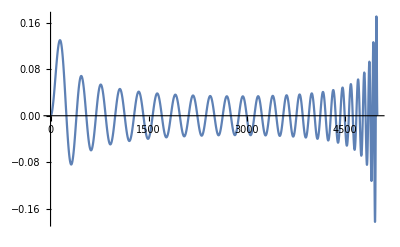

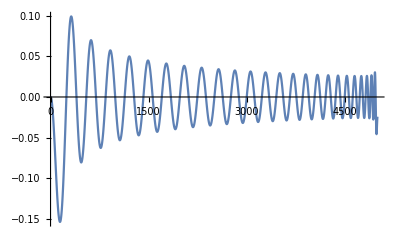

```mathematica
tabS = potentialList[Subscript[N, max],2];
tabD = densityList[Subscript[N, max],2];
ListPlot[tabD,Joined->True]
ListPlot[tabS,Joined->True]
```

```mathematica
outputList =Table[If[EvenQ[i], potentialList[Quotient[i,2], ℓ], densityList[Quotient[i,2], ℓ]] ,
{i,0,2 Subscript[N, max]+1}];
Export[filepath, outputList];
```

Because I can’t figure out how to do it, please output the param values ‘By hand’. They need to be in the order (please remember no commas!)

```mathematica
{Subscript[N, max], ℓ,N[ Subscript[N, step]], Subscript[R, ka]}
```

{48,2,0.0002,20}